```mathematica
(*Import the data*)
```

```mathematica
data=Import["./Downloads/qmp4023final.csv","csv"];
```

```mathematica
(*for h4015*)
```

```mathematica
data1=Drop[Transpose[data],1];
```

```mathematica
(*Transpose data to select the top 15 species*)
```

```mathematica
total={};
Do[AppendTo[total,Total[Drop[data1[[n]],1]]],{n,2,Length[data1]}]
```

```mathematica
topx=15;
```

```mathematica
top15={};
Do[AppendTo[top15,data1[[Flatten[Position[total,TakeLargest[total,topx][[n]]]]+1]]],{n,1,topx}]
```

```mathematica
(*put all the information for plotting in one*)
```

```mathematica
all={};
AppendTo[all,Transpose[data][[1]]];Do[AppendTo[all,Flatten[top15[[n]]]],{n,1,topx}]
```

```mathematica
Length[top15]
```

15

```mathematica
Length[all]
```

16

```mathematica
(*add "other" for all the samples*)
```

```mathematica
repli2=Import["./Downloads/qpcr_after16srrna_normalization.csv","csv"];
```

```mathematica
all[[1]]
```

{,HSM67VDR,HSM6XRUL,HSM6XRUN,HSM6XRUR,HSM6XRQ8,HSM7CZ16,HSM7CZ18,HSM7CZ1A,HSM7CZ1C,HSM7CZ1E,HSM7CZ1G,HSM7J4HA,HSM7J4HC,HSM7J4HE,HSM7J4HG,HSM7J4HI,HSM7J4HK,HSM7J4KC,HSM7J4KG,HSM7J4KI,HSM7J4KK,HSM7J4KM}

```mathematica
Transpose[all][[5]]
```

{HSM6XRUR,10.1465,1.00795,0.637782,0.232259,0.331895,0.0397351,0.0348121,0.0973329,0.0119034,0.0831819,0.138063,0.017108,0.222696,0.0908104,0.0900708}

```mathematica
other={};
Do[AppendTo[other,repli2[[Flatten[Position[Transpose[repli2][[1]],Transpose[all][[n]][[1]]]]]][[1]][[2]]],{n,2,23}]
```

```mathematica
Position[Transpose[repli2][[1]],Transpose[all][[3]][[1]]]
```

{{3}}

```mathematica
repli2[[18]]
```

{HSM7J4HK,5.03398}

```mathematica
other={};
Do[AppendTo[other,repli2[[Flatten[Position[Transpose[repli2][[1]],Transpose[all][[n]][[1]]]]]][[1]][[2]]-Total[Drop[Transpose[all][[n]],1]]],{n,2,23}]
```

```mathematica
Transpose[all][[2]]
```

{HSM67VDR,0.,0.324422,0.0330102,0.0530668,0.0773437,0.0158716,0.,0.0101086,0.0106849,0.00167949,0.107531,0.,0.0115988,0.0421362,0.}

```mathematica
other
```

{0.397577,1.06568,10.2429,1.46012,0.625553,2.7995,10.0474,1.79224,0.000785006,0.120381,0.666523,5.25482,4.20498,0.205534,12.3952,1.56289,1.69938,2.29715,0.165212,12.5241,0.990244,14.6721}

```mathematica
all = Insert[all,Flatten[{"other",other}],2];
```

```mathematica
Length[all]
```

17

```mathematica
(*create the genus name for labeling*)
names=Drop[Transpose[all][[1]],1];
```

```mathematica
names1={};
AppendTo[names1,names[[1]]];
Do[AppendTo[names1,StringSplit[StringSplit[names[[n]],"|"][[7]],"__"][[2]]],{n,2,Length[names]}]
```

```mathematica
names1
```

{other,Prevotella_copri,Bacteroides_sp_4_3_47FAA,Faecalibacterium_prausnitzii,Bacteroides_massiliensis,Bacteroides_vulgatus,Alistipes_putredinis,Phascolarctobacterium_succinatutens,Eubacterium_rectale,Parabacteroides_merdae,Bacteroides_caccae,Paraprevotella_unclassified,Akkermansia_muciniphila,Subdoligranulum_unclassified,Bacteroides_stercoris,Barnesiella_intestinihominis}

```mathematica
StringSplit[StringSplit[names[[5]],"|"][[7]],"__"][[2]]
```

Bacteroides_massiliensis

```mathematica
StringSplit[names[[2]],"|"][[7]]
```

s__Prevotella_copri

```mathematica
(*Plotting*)
```

```mathematica
data=Drop[Transpose[Drop[all,1]],1];
```

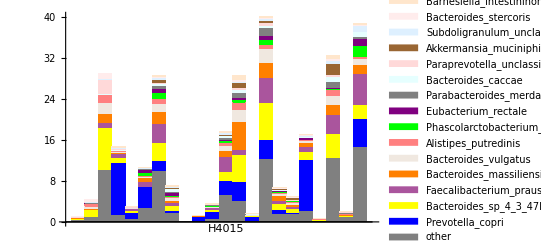

```mathematica
BarChart[data,ChartLabels->{{,,,,,,,,,,,"H4015",,,,,,,,,},None},
ChartLayout -> "Stacked",ChartStyle -> { Gray,Blue,Yellow,Blend[{Purple,LightYellow},1/3],Orange, LightBrown,Pink,Green, Purple, Gray,LightCyan,LightRed,Brown, LightBlue, LightPink,LightOrange},ChartLegends->names1,BaseStyle->{FontWeight->"Bold",FontSize->12},AxesStyle->Directive[Black,12]]
```